```mathematica
V[x_,y_,z_]:=(x^2+y^2+z^2)^(-1)+(100-(x^2+y^2+z^2))^(-1)
```

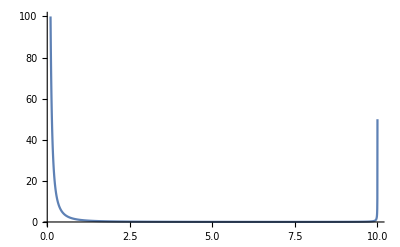

```mathematica
Plot[1/x^2+1/(100-x^2),{x,0.1,9.999},PlotRange->All]
```

```mathematica
gradV[x_,y_,z_]:={Evaluate[D[V[x,y,z],x]],Evaluate[D[V[x,y,z],y]],Evaluate[D[V[x,y,z],z]]}
```

```mathematica
gradV[x,y,z]
```

{(2 x)/((100-x^2-y^2-z^2)^2)-(2 x)/((x^2+y^2+z^2)^2),(2 y)/((100-x^2-y^2-z^2)^2)-(2 y)/((x^2+y^2+z^2)^2),(2 z)/((100-x^2-y^2-z^2)^2)-(2 z)/((x^2+y^2+z^2)^2)}

```mathematica
ft=20;
mysol=NDSolve[{x''[t]==-gradV[x[t],y[t],z[t]][[1]],y''[t]==-gradV[x[t],y[t],z[t]][[2]],z''[t]==-gradV[x[t],y[t],z[t]][[3]],x[0]==1,y[0]==1,z[0]==1,x'[0]==3/2,y'[0]==7/2,z'[0]==1/2},{x,y,z},{t,0,ft},WorkingPrecision->32,Method->{"TimeIntegration"->"ExplicitRungeKutta"}]
```

{{x→InterpolatingFunction[…],y→InterpolatingFunction[…],z→InterpolatingFunction[…]}}

```mathematica
mysol[[1]]
```

{x→InterpolatingFunction[…],y→InterpolatingFunction[…],z→InterpolatingFunction[…]}

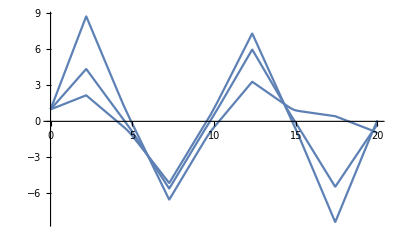

```mathematica
Plot[{x[t],y[t],z[t]} /. mysol,{t,0,ft}]
```

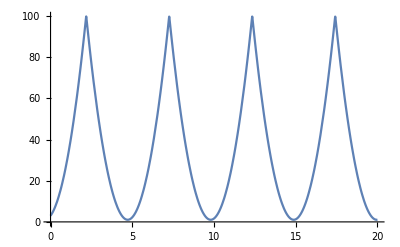

```mathematica
Plot[x[t]^2+y[t]^2+z[t]^2 /. mysol,{t,0,ft}]
```

```mathematica
l=Norm[Cross[{1,1,1},{3/2,7/2,1/2}]]
```

√14

```mathematica
rp0=D[Sqrt[x[t]^2+y[t]^2+z[t]^2],t] /. t->0 /. mysol
```

{3.1754264805429417048003182928}

```mathematica
Veff[r_]:=1/r^2 + 1/(100-r^2)+l^2/(2 r^2)
```

```mathematica
rsol=NDSolve[{r''[t]==-Veff'[r[t]],r[0]==Sqrt[3],r'[0]==rp0[[1]]},r[t],{t,0,ft}]
```

{{r[t]→InterpolatingFunction[…][t]}}

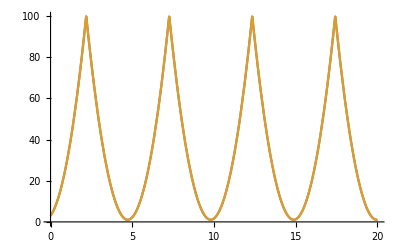

```mathematica
Plot[{x[t]^2+y[t]^2+z[t]^2 /. mysol,r[t]^2 /. rsol},{t,0,ft}]
```

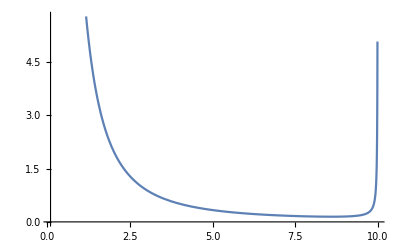

```mathematica
Plot[Veff[r],{r,0.1,9.99}]
```